## 1. Topological number

```mathematica
n={Cos[α[r,ϕ]] Sin[β[r,ϕ]],Sin[α[r,ϕ]] Sin[β[r,ϕ]],Cos[β[r,ϕ]]};
ddx=Cos[ϕ]D[n,r]-Sin[ϕ]/r D[n,ϕ];
ddy=Sin[ϕ]D[n,r]+Cos[ϕ]/r D[n,ϕ];
```

```mathematica
n.(ddx×ddy)//FullSimplify
```

(Sin[β[r,ϕ]] (-β^(0,1)[r,ϕ] α^(1,0)[r,ϕ]+α^(0,1)[r,ϕ] β^(1,0)[r,ϕ]))/r

```mathematica
Q=-1;
```

## 2. Classical hamiltonian

```mathematica
Npoints=500;
C1=1;(*exchange const*)
Dz=1;(*"Dm const*);
b = 0.6(*magnetic field const*)
tableB={};
err0=0.001;
k1=0.6;
fromR0=0.5;
toR0=8;
```

0.6

```mathematica
densEnergy=Table[
Setka=Table[N[R0/Npoints k],{k,1,Npoints}];
Setka=Prepend[Setka,err0];
beta=β/.NDSolve[{(Sin[β[r]] (b r^2+ C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+C1 r β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b) k1}} ]⟦1⟧;
wdens[r_]:=r (b-b Cos[beta[r]]+(Dz Cos[beta[r]] Sin[beta[r]])/r+(C1 Sin[beta[r]]^2)/(2 r^2)+Dz beta'[r]+1/2 C1 beta'[r]^2);
wdensTable=wdens[Setka];
W=2/(3 Npoints) Sum[ wdensTable⟦k-1⟧+4wdensTable⟦k⟧+wdensTable⟦k+1⟧,{k,2,Npoints,2}]/ R0;
{R0,W},{R0,fromR0,toR0,0.05}];
```

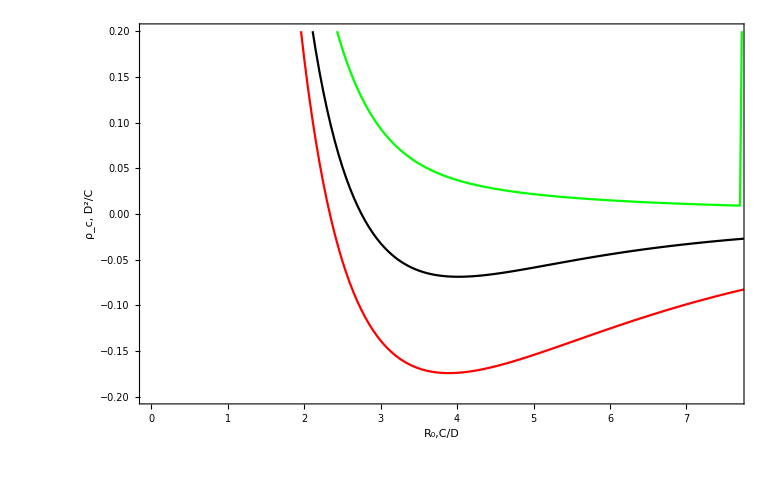

```mathematica
Show[

ListPlot[densEnergy2,PlotRange->{{0,7.6},{-0.2,0.2}},Frame->True,Joined->True,PlotStyle->Green,FrameLabel->{"R_0,C/D","ρ_c, D^2/C"},BaseStyle->{FontSize->16},FrameStyle->Directive[Black,Bold,Medium],PlotLegends->Placed[{"b=0.9"},{0.8,0.8}],PlotStyle->{Red,Thickness[0.002]},Joined->True,   BaseStyle->{FontSize->16}],

ListPlot[densEnergy3,PlotRange->{{0,7},{-0.2,0.2}},PlotLegends->Placed[{"b=0.4"},{0.8,0.8}],Frame->True,Joined->True,PlotStyle->Red,FrameLabel->{"R_0,C/D","ρ_c, D^2/C"},Joined->True,   BaseStyle->{FontSize->16}],
ListPlot[densEnergy,PlotRange->{{0,7},{-0.2,0.2}},PlotLegends->Placed[{"b=0.6"},{0.8,0.8}],Frame->True,Joined->True,PlotStyle->Black,FrameLabel->{"R_0,C/D","ρ_c, D^2/C"},PlotStyle->{Black,Thickness[0.002]},Joined->True,   BaseStyle->{FontSize->16}]

]
```

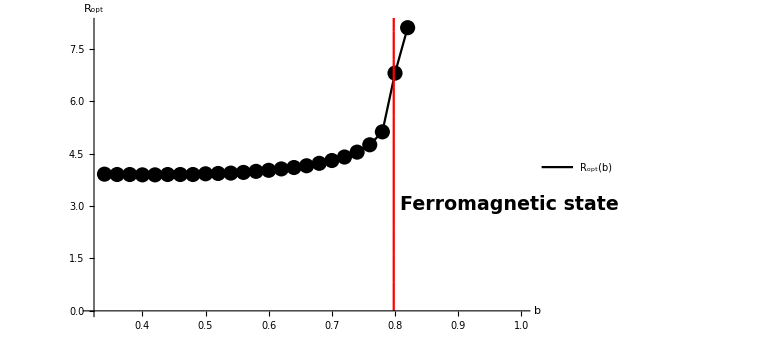

## 3. WKB derivate quantum hamiltonian:

```mathematica
Uo1=({{Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ], -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ], Cos[α] Sin[β]}, {Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ], Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ], Sin[α] Sin[β]}, {-Cos[γ] Sin[β], Sin[β] Sin[γ], Cos[β]}})/.{γ->α};
```

```mathematica
X2=({{1/4 (-4 (Cos[γ]^2 Dt[β,x]^2+Dt[γ,x]^2)-Dt[α,x]^2 (3+Cos[2 β]-2 Cos[2 γ] Sin[β]^2)-8 Dt[α,x] (Cos[β] Dt[γ,x]+Cos[γ] Dt[β,x] Sin[β] Sin[γ])), -Cos[β] Dt[α,{x,2}]-Dt[γ,{x,2}]+Sin[γ] (Cos[γ] (Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2)+2 Dt[α,x] Dt[β,x] Sin[β] Sin[γ]), Cos[γ] (Dt[β,{x,2}]-Cos[β] Dt[α,x]^2 Sin[β])+(2 Cos[β] Dt[α,x] Dt[β,x]+Dt[α,{x,2}] Sin[β]) Sin[γ]}, {Cos[β] Dt[α,{x,2}]+Dt[γ,{x,2}]+Cos[γ] (-2 Cos[γ] Dt[α,x] Dt[β,x] Sin[β]+(Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2) Sin[γ]), 1/4 (-Dt[α,x]^2 (3+Cos[2 γ]+2 Cos[2 β] Sin[γ]^2)-4 (Dt[γ,x]^2+Dt[β,x]^2 Sin[γ]^2)+Dt[α,x] (-8 Cos[β] Dt[γ,x]+4 Dt[β,x] Sin[β] Sin[2 γ])), 2 Cos[β] Cos[γ] Dt[α,x] Dt[β,x]+Cos[γ] Dt[α,{x,2}] Sin[β]-Dt[β,{x,2}] Sin[γ]+Cos[β] Dt[α,x]^2 Sin[β] Sin[γ]}, {-Cos[γ] (Dt[β,{x,2}]+Dt[α,x] (Cos[β] Dt[α,x]+2 Dt[γ,x]) Sin[β])+(2 Dt[β,x] Dt[γ,x]-Dt[α,{x,2}] Sin[β]) Sin[γ], 2 Cos[γ] Dt[β,x] Dt[γ,x]-Cos[γ] Dt[α,{x,2}] Sin[β]+(Dt[β,{x,2}]+Dt[α,x] (Cos[β] Dt[α,x]+2 Dt[γ,x]) Sin[β]) Sin[γ], -Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2}})/.{γ->α};
```

```mathematica
X1={{0,-Cos[β] Dt[α,x]-Dt[γ,x],Cos[γ] Dt[β,x]+Dt[α,x] Sin[β] Sin[γ]},{Cos[β] Dt[α,x]+Dt[γ,x],0,Cos[γ] Dt[α,x] Sin[β]-Dt[β,x] Sin[γ]},{-Cos[γ] Dt[β,x]-Dt[α,x] Sin[β] Sin[γ],-Cos[γ] Dt[α,x] Sin[β]+Dt[β,x] Sin[γ],0}}/.{γ->α};
delrot={Dt[β,r[1]]->  Cos[ϕ]Dt[β,r]-Sin[ϕ]/r  Dt[β,ϕ], 
Dt[α,r[1]]->  Cos[ϕ]Dt[α,r]-Sin[ϕ]/r  Dt[α,ϕ],
Dt[β,r[2]]->Sin[ϕ]Dt[β,r]+Cos[ϕ]/r  Dt[β,ϕ],
Dt[α,r[2]]->Sin[ϕ]Dt[α,r]+Cos[ϕ]/r  Dt[α,ϕ] };
```

```mathematica
χ1=s Sum[(r[l]X1/.x->r[l]),{l,1,2}]/.delrot/.{r[1]->r1 Cos[ϕ1],r[2]->r1 Sin[ϕ1]}/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{α->ϕ-Subscript[α, 0],β->β[r]}//FullSimplify;
ex={β'[r]->D[2 ArcTan[1/r],r]//FullSimplify, β[r]->2 ArcTan[1/r]};
```

```mathematica
S1={(√(2s))/2(ap+a),-ⅈ(√(2s))/2(a-ap),s-ap a};
S2={(√s (a+ap))/(√2),-(ⅈ √s (a-ap))/(√2),-ap a};
```

```mathematica
DMi1=Table[Subscript[D, z] Sum[Signature[{i,k,l}](X1⟦k,j⟧/.{x->r[m]})Uo1⟦m,l⟧,{k,3},{m,2},{l,3}],{i,3},{j,3}]//Simplify;
```

```mathematica
Unew=Dt[Uo1,x];
```

```mathematica
DMi2=Table[-Subscript[D, z] Sum[Signature[{a,b,c}](Unew⟦e,c⟧/.{x->r[e]}),{c,3},{e,2}],{a,3},{b,3}]//Simplify;
```

```mathematica
DM1=DMi1/.delrot/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{β->β[r]}/.{α->ϕ+αo}//FullSimplify;
```

```mathematica
DM2=DMi2/.delrot/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{β->β[r]}/.{α->ϕ+αo}//FullSimplify;
```

```mathematica
Sa={1/2 √(2 s) (a+ap),1/2 (-ⅈ) √(2 s) (a-ap),s-ap a};

Sdt=FullSimplify[Dt[Sa,x]/.Dt[s,x]->0];
Dt[Sa,x];
UU=Uo1;
US=Table[Sum[UU[[e,c]](Sdt[[b]]/.{x->r[e]}),{e,2}],{c,3},{b,3}]/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ] }//FullSimplify;
GradCoef1=(Subscript[D, z] Sum[Signature[{i,k,l}]Sa[[i]]US[[l,k]],{i,3},{k,3},{l,3}])/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef2=(-C( (Sum[Sa[[k]](X1[[k,i]]/.{ x->r[e]})(Sdt[[i]]/.{x->r[e]}),{e,2},{k,3},{i,3}])/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ]}/.{delrot}))/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef1parts=-Subscript[D, z] (Sum[Signature[{i,k,l}]S2[[i]]US[[l,k]],{i,3},{k,3},{l,3}])/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef2parts=C( (Sum[(Sdt[[k]]/.{x->r[e]})(X1[[k,i]]/.{x->r[e]})S2[[i]],{e,2},{k,3},{i,3}])/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ]}/.{delrot})/.{α->ϕ+αo,β->β[r]};
```

```mathematica
Grad3=-C/2 S1.Dt[S1,{x,2}]/.{Dt[a,{x,2}]->Δa,Dt[ap,{x,2}]->Δap,Dt[ap,x]->∇ap,Dt[a,x]->∇a , Dt[s,x]->0,  Dt[s,{x,2}]->0};
```

```mathematica
Hex1=-C/2(X2/.{Dt[β,x]->∇β,Dt[α,x]-> ∇α, Dt[α,{x,2}]-> Δα, Dt[β,{x,2}]-> Δβ}//Expand)/. {Δα->0,∇α ∇β->0,(∇α)^2->1/r^2}//Simplify;
```

```mathematica
Hex2tmp1=C Dt[X1,x]//FullSimplify;
Hex2tmp2=Hex2tmp1/.{Dt[β,x]->∇β,Dt[α,x]-> ∇α, Dt[α,{x,2}]-> Δα, Dt[β,{x,2}]-> Δβ}//Expand;
Hex2=Hex2tmp2//.{Δα->0,∇α ∇β->0,(∇α)^2->1/r^2};
```

```mathematica
U1=(Hex1/.{ Δβ->Dt[β,{r,2}]+Dt[β,r]/r,∇β->Dt[β,r]})/.{β->β[r], α->ϕ+αo}//FullSimplify;
U2=(Hex2/.{ Δβ->Dt[β,{r,2}]+Dt[β,r]/r,∇β->Dt[β,r]})/.{β->β[r], α->ϕ+αo}//FullSimplify;
Uo=Uo1/.{α->ϕ+αo,β->β[r]};


X=U1⟦1,3⟧+DM1⟦1,3⟧-b /2Uo⟦3,1⟧+ⅈ(U1⟦2,3⟧+DM1⟦2,3⟧-b/2 Uo⟦3,2⟧)/.{αo->-π/2, Dt[ϕ,r]->0};
```

```mathematica
ddbeta2=(Solve[X==0,β''[r]]//FullSimplify)[[1]];
```

```mathematica
HamiltDMI=(Grad3+GradCoef1+GradCoef2+S1.U1.S1+S1.DM1.S1- b s Uo[[3]].S1)/.ddbeta2/.{αo->-π/2, Dt[ϕ,r]->0};
```

```mathematica
Coefficient[HamiltDMI, s^2]//Expand
```

{-b Cos[β[r]]+(C Sin[β[r]]^2)/(2 r^2)+(Cos[β[r]] Sin[β[r]] D_z)/r+D_z β'[r]+1/2 C β'[r]^2}

Now s^3/2 not 0 but after integration by parts hamiltonian become equal to 0:

```mathematica
HamilByParts=(Grad3+GradCoef1parts+GradCoef2parts+S1.U1.S1+S1.DM1.S1+S1.U2.S2+S1.DM2.S2- b s Uo[[3]].S1)/.{β''[r]->(Sin[β[r]] (C Cos[β[r]]+2 r (b/2 r+Subscript[D, z] Sin[αo] Sin[β[r]]))-r (C+2 ⅈ Subscript[D, z] r Cos[αo] Sin[β[r]]) β'[r])/(C r^2)}/.{αo->-π/2};
Coefficient[HamilByParts, s^(3/2)]/.{Dt[a,ϕ]-> ⅈ m a, Dt[ap,ϕ]->-ⅈ m ap}//FullSimplify
```

{0}

```mathematica
H=Coefficient[HamiltDMI, s]/.{ Dt[a,ϕ]->-ⅈ Lz a, Dt[ap,ϕ]-> ⅈ Lz ap}//FullSimplify//Expand;
```

```mathematica
H/.{ap->SuperDagger[a]}
```

```mathematica
aaplus=Coefficient[C ∇a ∇SuperDagger[a]+(a^2 C ⅇ^(2 ⅈ ϕ) Sin[β[r]]^2)/(4 r^2)+(a^2 ⅇ^(2 ⅈ ϕ) Sin[2 β[r]] Subscript[D, z])/(4 r)+(5 a C SuperDagger[a])/(4 r^2)-(2 a C Lz SuperDagger[a])/r^2+a b Cos[β[r]] SuperDagger[a]+(2 a C Cos[β[r]] SuperDagger[a])/r^2-(2 a C Lz Cos[β[r]] SuperDagger[a])/r^2+(3 a C Cos[2 β[r]] SuperDagger[a])/(4 r^2)-(2 a Sin[β[r]] Subscript[D, z] SuperDagger[a])/r+(2 a Lz Sin[β[r]] Subscript[D, z] SuperDagger[a])/r-(3 a Sin[2 β[r]] Subscript[D, z] SuperDagger[a])/(2 r)+(C ⅇ^(-2 ⅈ ϕ) Sin[β[r]]^2 (SuperDagger[a])^2)/(4 r^2)+(ⅇ^(-2 ⅈ ϕ) Sin[2 β[r]] Subscript[D, z] (SuperDagger[a])^2)/(4 r)-1/2 a^2 ⅇ^(2 ⅈ ϕ) Subscript[D, z] β'[r]-a Subscript[D, z] SuperDagger[a] β'[r]-1/2 ⅇ^(-2 ⅈ ϕ) Subscript[D, z] (SuperDagger[a])^2 β'[r]-1/4 a^2 C ⅇ^(2 ⅈ ϕ) β'[r]^2-1/2 a C SuperDagger[a] β'[r]^2-1/4 C ⅇ^(-2 ⅈ ϕ) (SuperDagger[a])^2 β'[r]^2, SuperDagger[a] SuperDagger[a]] SuperDagger[a] SuperDagger[a]

aa=Coefficient[C ∇a ∇SuperDagger[a]+(a^2 C ⅇ^(2 ⅈ ϕ) Sin[β[r]]^2)/(4 r^2)+(a^2 ⅇ^(2 ⅈ ϕ) Sin[2 β[r]] Subscript[D, z])/(4 r)+(5 a C SuperDagger[a])/(4 r^2)-(2 a C Lz SuperDagger[a])/r^2+a b Cos[β[r]] SuperDagger[a]+(2 a C Cos[β[r]] SuperDagger[a])/r^2-(2 a C Lz Cos[β[r]] SuperDagger[a])/r^2+(3 a C Cos[2 β[r]] SuperDagger[a])/(4 r^2)-(2 a Sin[β[r]] Subscript[D, z] SuperDagger[a])/r+(2 a Lz Sin[β[r]] Subscript[D, z] SuperDagger[a])/r-(3 a Sin[2 β[r]] Subscript[D, z] SuperDagger[a])/(2 r)+(C ⅇ^(-2 ⅈ ϕ) Sin[β[r]]^2 (SuperDagger[a])^2)/(4 r^2)+(ⅇ^(-2 ⅈ ϕ) Sin[2 β[r]] Subscript[D, z] (SuperDagger[a])^2)/(4 r)-1/2 a^2 ⅇ^(2 ⅈ ϕ) Subscript[D, z] β'[r]-a Subscript[D, z] SuperDagger[a] β'[r]-1/2 ⅇ^(-2 ⅈ ϕ) Subscript[D, z] (SuperDagger[a])^2 β'[r]-1/4 a^2 C ⅇ^(2 ⅈ ϕ) β'[r]^2-1/2 a C SuperDagger[a] β'[r]^2-1/4 C ⅇ^(-2 ⅈ ϕ) (SuperDagger[a])^2 β'[r]^2, a a]a a 

(H/.{ap->SuperDagger[a]})- aa -aaplus//FullSimplify//Expand
```

(a^†)^2 ((C ⅇ^(-2 ⅈ ϕ) Sin[β[r]]^2)/(4 r^2)+(ⅇ^(-2 ⅈ ϕ) Sin[2 β[r]] D_z)/(4 r)-1/2 ⅇ^(-2 ⅈ ϕ) D_z β'[r]-1/4 C ⅇ^(-2 ⅈ ϕ) β'[r]^2)

a^2 ((C ⅇ^(2 ⅈ ϕ) Sin[β[r]]^2)/(4 r^2)+(ⅇ^(2 ⅈ ϕ) Sin[2 β[r]] D_z)/(4 r)-1/2 ⅇ^(2 ⅈ ϕ) D_z β'[r]-1/4 C ⅇ^(2 ⅈ ϕ) β'[r]^2)

{C ∇a ∇a^†+(5 a C a^†)/(4 r^2)-(2 a C Lz a^†)/r^2+a b Cos[β[r]] a^†+(2 a C Cos[β[r]] a^†)/r^2-(2 a C Lz Cos[β[r]] a^†)/r^2+(3 a C Cos[2 β[r]] a^†)/(4 r^2)-(2 a Sin[β[r]] D_z a^†)/r+(2 a Lz Sin[β[r]] D_z a^†)/r-(3 a Cos[β[r]] Sin[β[r]] D_z a^†)/r-a D_z a^† β'[r]-1/2 a C a^† β'[r]^2}

## 4. Algorithm for solve:

```mathematica
err0=0.0001;
kk1=0.9;
maxMode=4; (*Magnet quantum number m*)
Nsize=60; (*Size of matrix*)
Npoints=Nsize×7;
C1=1;(*C*)
b=0.4; (*Magnetic field*)
Dz=1; (*Dzyaloshiskiy-Morya interaction const*)
m=1;
tableB={{0.12,4.1},{0.14,4.08},{0.16,4.05},{0.18,4.03},{0.2,4.},{0.22,3.99},{0.24,3.9699999999999998},{0.26,3.95},{0.28,3.94},{0.3,3.93},{0.32,3.91},{0.34,3.91},{0.36,3.9},{0.38,3.9},{0.4,3.89},{0.42,3.89},{0.44,3.9},{0.46,3.9},{0.48,3.9},{0.5,3.92},{0.52,3.93},{0.54,3.94},{0.56,3.96},{0.58,3.99},{0.6,4.02},{0.62,4.0600000000000005},{0.64,4.1},{0.66,4.15},{0.68,4.22},{0.7,4.3},{0.72,4.4},{0.74,4.54},{0.76,4.75},{0.78,5.12},{0.8,6.800000000000001},{0.82,8.100000000000001}};
R0=Select[tableB,#⟦1⟧==b&]⟦1,2⟧;
```

```mathematica
Setka=Table[N[R0/Npoints k],{k,1,Npoints}];
Setka=Prepend[Setka,err0];

λn1[n_]:=(BesselJZero[(m+1),n]/R0)^2;
ϕn1[n_,r_]:=Sqrt[2]/Abs[R0((D[BesselJ[(m+1),rr1],rr1])/.rr1->BesselJZero[(m+1),n])]BesselJ[(m+1),BesselJZero[(m+1),n] /R0  r];


λn2[n_]:=(BesselJZero[(m-1),n]/R0)^2;
ϕn2[n_,r_]:=Sqrt[2]/Abs[R0 ((D[BesselJ[(m-1),rr1],rr1])/.rr1->BesselJZero[(m-1),n]) ]BesselJ[(m-1),BesselJZero[(m-1),n] /R0  r];


matrxϕn1=Table[ϕn1[k,Setka],{k,1,Nsize}];(*It's the hardest part of computation*)
matrxϕn2=Table[ϕn2[k,Setka],{k,1,Nsize}];

beta=β/.NDSolve[{(Sin[β[r]] (b r^2+Cos[β[r]]-2 Dz r Sin[β[r]]))/r==β'[r]+r β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)err0 , β'[err0] == -√(b) }} ]⟦1⟧;

βmin[r_]:=beta[r];
dβmin[r_]:=beta'[r];

funcV0[r_]:=r(b Cos[βmin[r]]+(3 C1 (Cos[2 βmin[r]]-1))/(4 r^2)-(3 Dz Cos[βmin[r]] Sin[βmin[r]])/r-Dz dβmin[r]-1/2 C1( dβmin[r])^2);
funcV1[r_]:=r(-(2 C1 (Cos[βmin[r]]+1))/r^2+(2 Dz Sin[βmin[r]])/r);
funcG[r_]:=r((C1 Sin[βmin[r]]^2)/(2 r^2)+(Dz Sin[2βmin[r]])/(2 r)-Dz dβmin[r]-1/2 C1 (dβmin[r])^2);


pointsFuncV0=funcV0[Setka];
pointsFuncV1=funcV1[Setka];
pointsFuncG=funcG[Setka];

(*It's Simpson's rule*)

 F1[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 λn1[k1]+R0/(3 Npoints) Sum[ matrxϕn1⟦k1,k-1⟧
matrxϕn1⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧+m pointsFuncV1⟦k-1⟧)+
4matrxϕn1⟦k1,k⟧matrxϕn1⟦k2,k⟧(pointsFuncV0⟦k⟧+m pointsFuncV1⟦k⟧)+
matrxϕn1⟦k1,k+1⟧matrxϕn1⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧+m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 F2[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 λn2[k1]+R0/(3 Npoints) Sum[ matrxϕn2⟦k1,k-1⟧
matrxϕn2⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧-m pointsFuncV1⟦k-1⟧)+4matrxϕn2⟦k1,k⟧
matrxϕn2⟦k2,k⟧(pointsFuncV0⟦k⟧-m pointsFuncV1⟦k⟧)+matrxϕn2⟦k1,k+1⟧
matrxϕn2⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧-m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 G[k1_,k2_]:=R0/(3 Npoints) Sum[ 
matrxϕn1⟦k1,k-1⟧matrxϕn2⟦k2,k-1⟧pointsFuncG⟦k-1⟧+
4matrxϕn1⟦k1,k⟧matrxϕn2⟦k2,k⟧pointsFuncG⟦k⟧+
matrxϕn1⟦k1,k+1⟧matrxϕn2⟦k2,k+1⟧pointsFuncG⟦k+1⟧,{k,2,Npoints,2}];

     F1table=Table[If[i<=j,F1[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F1table⟦k,i⟧=F1table⟦i,k⟧])
];

     F2table=Table[If[i<=j,F2[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F2table⟦k,i⟧=F2table⟦i,k⟧])
];

 Gtable=Table[If[i<=j,G[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,Gtable⟦k,i⟧=Gtable⟦i,k⟧])
];

matrixHdG=ArrayFlatten[{{F1table, Gtable}, {-Gtable, -F2table}}];

matrixHdG2=ArrayFlatten[{{F1table⟦1;;Nsize-10,1;;Nsize-10⟧, Gtable⟦1;;Nsize-10,1;;Nsize-10⟧}, {-Gtable⟦1;;Nsize-10,1;;Nsize-10⟧, -F2table⟦1;;Nsize-10,1;;Nsize-10⟧}}];

tmpmoda=Eigenvalues[matrixHdG2];
moda0=Eigenvalues[matrixHdG];
Do[If[Im[Chop[moda0⟦i⟧]]>err0,Print["There is a complex value! R_0=",R0,", E[",i,"]=",moda0⟦i⟧] ],{i,1,2 Nsize}];

If[Length[Select[moda0,#>0&]]==Length[Select[moda0,#<0&]],Print["Number of positive values equals to number of negative ones"],Print["Alarm!!! Number of positive values NOT equals to number of negative ones"]];

mPositive=Sort[Select[moda0,#>0&],Abs[#1]<Abs[#2]&];
mNegative=Sort[Select[moda0,#<0&],Abs[#1]<Abs[#2]&];
tmpPos=Sort[Select[tmpmoda,#>0&],Abs[#1]<Abs[#2]&];
tmpNeg=Sort[Select[tmpmoda,#<0&],Abs[#1]<Abs[#2]&];

moda0=mPositive;
tmpmoda=tmpPos;

Print["m is ", m];
Print["R_0 is ", R0];
Print["Error=",Max[Table[Abs[moda0⟦k⟧-tmpmoda⟦k⟧],{k,1,(Nsize-15)}]]] ;
Print[tmpmoda⟦1;;8⟧ ," for N = ", Nsize-10];
Print[moda0⟦1;;8⟧," for N = ", Nsize];


If[m≠0,QuantumCorrections=Sum[Abs[mPositive⟦i⟧]+Abs[mNegative⟦i⟧],{i,1,Nsize}]-Sum[F1table⟦i,i⟧ +F2table⟦i,i⟧ ,{i,1,Nsize}],
QuantumCorrections=0.5 (Sum[Abs[moda0⟦i⟧],{i,1,Nsize}]-Sum[F1table⟦i,i⟧ +F2table⟦i,i⟧ ,{i,1,Nsize}])];
Print["Eqс = ", QuantumCorrections];
```

Number of positive values equals to number of negative ones

m is 1

R_0 is 3.89

Error=3.88598×10^-8

{2.04662,5.51125,9.86787,15.4516,22.3196,30.4836,39.9479,50.7143}for N = 50

{2.04662,5.51125,9.86787,15.4516,22.3196,30.4836,39.9479,50.7143}for N = 60

Eqm = -0.634447